# Stylized facts in financial time series

Stylized facts are statistical properties emerging from the returns of financial time series that are present in almost every market.

## Getting stylized facts from an index

Although the mechanism which generates the financial time series it is not fully understood, making impossible to have a prediction on the next stock price, there are however some statistical properties inherent to the financial time series, these are called stylized facts. We can explore them using the FinancialData function, that conveniently can load the stock prices and returns.

Stylized facts are the result of many independent empirical studies on the statistical properties of financial markets that have been proven to be common across financial markets.

This is how a financial time series usually look like: Random, noisy and in some cases similar to a random walk. In this case since we are using an index that tracks the most successful companies in an stock market it has a tendency of growth.

We will start this exploration using the Mexican index IPC because it has had a growth in efficiency that can be seen in the stylized facts.

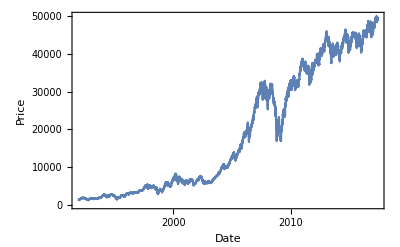

```mathematica
DateListPlot[FinancialData["^MXX",All],PlotRange->Full,FrameLabel->{"Date","Price"}]
```

To get the stylized facts we need to compute the returns, that are a stationary measure of the price changes. Returns are defined as the price difference in a timespan.

```mathematica
returns = FinancialData["^MXX","Return",All];
```

Let’s plot them

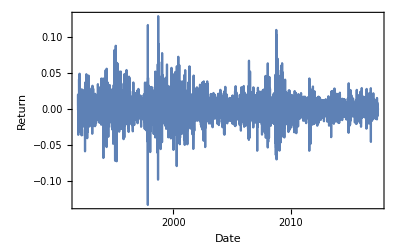

```mathematica
DateListPlot[returns,PlotRange->Full,Frame->True,FrameLabel->{"Date","Return"}]
```

The first stylized fact is that returns lack autocorrelations. This is actually to be expected in an efficient market, because present prices have to reflect all information that is currently know of the market (assuming that investors are rational), making impossible to make a future prediction because the expected value of the future price would have to be the present price.

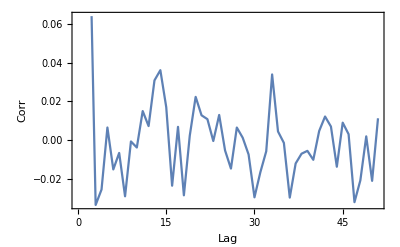

```mathematica
dates = returns[[All,1]]; values = returns[[All,2]];
ListLinePlot[CorrelationFunction[values,{50}],Frame->True,FrameLabel->{"Lag","Corr"}]
```

But investors are not always rational, so autocorrelation in fact can be used to as an indicator of the efficiency of the market. More efficient markets often are less autocorrelated.

We can plot the same data in different time windows and look at the value of autocorrelation at lag = 2. As time passes this market becomes more efficient.

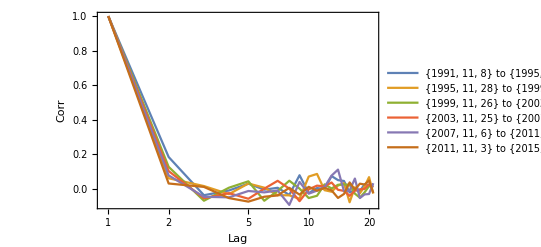

```mathematica
ListPlot[Map[CorrelationFunction[#,{20}]&,Partition[values,1000]],Joined->True,ScalingFunctions->{"Log",None},PlotRange->Full,PlotLegends->Map[ToString[First[#]]<>" to "ToString[Last[#]]&,Partition[dates,1000]],Frame->True,FrameLabel->{"Lag","Corr"}]
```

Because autocorrelation functions were originally developed as a tool for modelling dependence between linear models and Gaussian time series, when applying autocorrelation to a financial time series which has heavy tails one has to note that they might not very reliable.

Returns are characterized for having heavy tails. A simple way to view this fact is to plot the histogram in a logarithmic vertical scale. Since the distribution is a power law we will see most values of the histogram aligning. In some cases there could be some events with abnormally large values that can’t be described by a power law. These are often indicators of an economic crisis.

Notice that we are taking the positive values of the returns. One can also do exactly the same analysis the the negative part of the distribution.

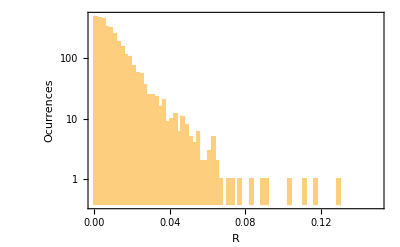

```mathematica
positiveValues = Select[returns,Last[#]≥0&];
Histogram[positiveValues[[All,2]],ScalingFunctions->{None,"Log"},PlotRange->{{0,0.15},All},Frame->True,FrameLabel->{"R","Ocurrences"}]
```

Notice that if we are to assume that the tail in fact decay as a power law, there are still some events that should have almost zero probability of happening but they still appear. These outliers are commonly referred to as Dragon-Kings because they are not to be dismissed, actually their presence might be an indication of a big state transition of the market that could lead to a market crash.

It seems worth investigating these outliers and one way to select them is to use the Anderson-Darling statistic of a power law distribution to find the point γ_right from where the extreme events begin.

Also the Anderson-Darling statistic is a nice way to select the point γ_left from where the power-law tail begin.

```mathematica
AndersonDarling[data_,γ_]:= Block[{s, n,α,z,A2},
s = Sort[data];
n = Count[s,x_/;x≥γ];
If[n>1,
s = s[[-n;;-1]];
α = (1/n Sum[Log[s[[i]]/γ],{i,1,n}])^-1;
z = Table[1-(γ/s[[i]])^α,{i,1,n}];
A2 = -n-1/n Sum[(2i-1)(Log[z[[i]]]+Log[1-z[[n-i+1]]]),{i,1,n}]; 
Return[A2];,
Return[∞];
];
];
LeftCutoff[data_,γmin_,γmax_,dγ_]:=Block[{tbl,minPos},
tbl = Table[{γ,AndersonDarling[data,γ]},{γ,γmin,γmax,dγ}];
tbl = DeleteCases[tbl,{_,∞}];
minPos =Position[tbl[[All,2]],Min[tbl[[All,2]]]][[1,1]];
Return[tbl[[minPos,1]]];
];
RightCutoff[data_,γmin_,γmax_,dγ_]:=Block[{tbl,maxPos,left},
left = LeftCutoff[data,γmin,γmax,dγ];
tbl = Table[{γ,AndersonDarling[data,γ]},{γ,γmax,left,-dγ}];
tbl = DeleteCases[tbl,{_,∞}];
maxPos =Position[tbl[[All,2]],Max[tbl[[All,2]]]][[1,1]];
Return[tbl[[maxPos,1]]];
];
```

We can then select the point γ_left from where the power law tail begin

```mathematica
γleft = LeftCutoff[positiveValues[[All,2]],0.01,0.08,0.0001]
```

0.0455

And the point γ_right from where the extreme events begin

```mathematica
γright = RightCutoff[positiveValues[[All,2]],0.01,0.08,0.0001]
```

0.0633

And to visualize them better we add those points as vertical gridlines

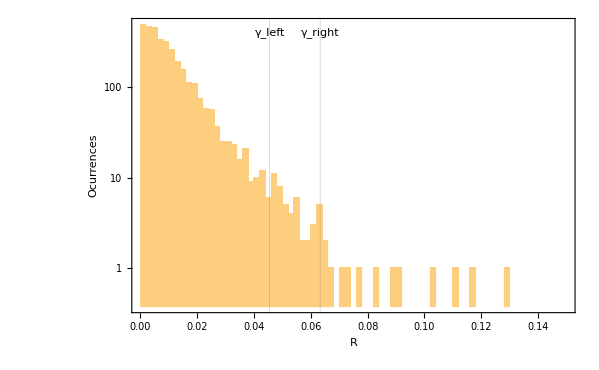

```mathematica
Histogram[positiveValues[[All,2]],ScalingFunctions->{None,"Log"},PlotRange->{{0,0.15},All},GridLines->{{γleft,γright},None},Frame->True,FrameLabel->{"R","Ocurrences"},Epilog->{Inset[Text["γ_left"],{γleft,6}],Inset[Text["γ_right"],{γright,6}]}]
```

To make sure we found the right γ point we can just tell Mathematica to find the distribution of the points right from γ_left.

```mathematica
FindDistribution[Select[returns[[All,2]], #>γleft&]]
```

ParetoDistribution[7.,49.4139,1.64916,0.0455895]

Now we have a list of extreme events with their dates

```mathematica
extremeEvents = Select[positiveValues,Last[#]>γright&];
Grid[{{"Date","Price change"}}~Join~extremeEvents,Frame->All]
```

Date | Price change
{1994,12,22} | 0.0821327
{1995,1,31} | 0.0880388
{1995,3,10} | 0.0642549
{1995,3,24} | 0.06331
{1997,10,28} | 0.116888
{1998,9,15} | 0.12923
{1998,9,23} | 0.0908015
{1998,10,15} | 0.0655278
{1999,1,15} | 0.0778111
{2000,6,2} | 0.0727218
{2006,6,15} | 0.0672672
{2008,1,22} | 0.0635898
{2008,10,13} | 0.110052
{2008,10,28} | 0.103102
{2008,11,24} | 0.0700132
{2009,4,13} | 0.0637258

We can plot the dates that correspond to the extreme events.

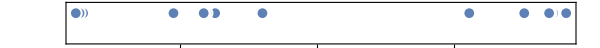

```mathematica
TimelinePlot[extremeEvents[[All,1]]]
```

Notice that most of them are packed together and all of them are around known market crashes, so we can use FindClusters to find which extreme events correspond to a known market crash.

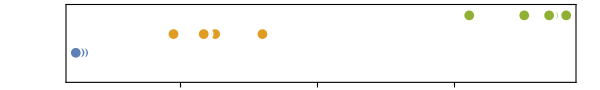

```mathematica
TimelinePlot[FindClusters[Map[DateObject,extremeEvents[[All,1]]],3]]
```

Distributions are often asymmetrical around the origin, this is considered an stylized fact. One way to test this is to use the T_n statistic which can be implemented with the following code.

```mathematica
Tn[Y_]:= Module[{n,X,loglik,kx,fnleft,fnminus},
n = Length[Y];
X = Sort[Y];
loglik =Sum[
kx = Abs[X[[i]]];
fnleft = Count[X, x_/;x<kx];
fnminus = Count[X, x_/;x≤ -kx];
Piecewise[{{fnminus*Log[(fnminus+n-fnleft)/(2 fnminus)],fnminus>0},{0,fnminus ≤ 0}}]+Piecewise[{{(n-fnleft)*Log[(fnminus+n-fnleft)/(2(n-fnleft))],fnleft < n},{0,fnleft ≥ n}}]
,{i,1,n}
];
Return[N[-(2loglik)/n]];
];
Tn[Y_,c_]:=Tn[Y-c];

αs = {0.001,0.005,0.01,0.025,0.05,0.1,0.15,0.25,0.5};
qs = {7.803,5.768,4.909,3.798,2.983,2.200,1.768,1.258,0.659};
αq = Transpose[{αs,qs}];
upp = Interpolation[αq];
UpperPercentagePoint[p_]:= upp[p];
```

Then to test the symmetry around the origin we evaluate the T_n statistic and check if it’s value is under the confidence interval.

Since the Mexican market it’s not as efficient as US markets, making it more symmetric we will showcase this behavior using the S&P 500 index. Also because this method it’s computationally expensive we will use a sub sample of 1000 values of the returns.

```mathematica
returns = FinancialData["^GSPC","Return",All];
smallreturnssample = Take[returns[[All,2]],1000];
confidenceInterval = 0.95;
If[Tn[smallreturnssample,0] < UpperPercentagePoint[1-confidenceInterval],"Symmetric","Assymetric"]
```

Assymetric

If we are interested in checking where is the most plausible point of symmetry we can compute the T_n statistic in multiple symmetry test points c.

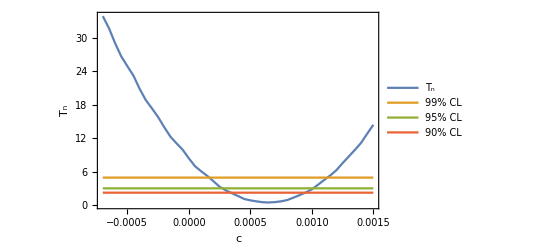

```mathematica
returns = FinancialData["^GSPC","Return",All];
smallreturnssample = Take[returns[[All,2]],1000];
cmin = -0.0007;
cmax = 0.0015;
Δc = 0.00005;
sim = Table[{c,Tn[smallreturnssample,c]},{c,cmin,cmax,Δc}];

upp1 = {{cmin, UpperPercentagePoint[0.01]},{cmax,UpperPercentagePoint[0.01]}};
upp2 = {{cmin, UpperPercentagePoint[0.05]},{cmax,UpperPercentagePoint[0.05]}};
upp3 = {{cmin, UpperPercentagePoint[0.1]},{cmax,UpperPercentagePoint[0.1]}};

ListPlot[{sim,upp1,upp2,upp3},Joined->True,Frame->True,FrameLabel->{"c","T_n"},PlotLegends->{"T_n","99% CL","95% CL","90% CL"}]
```

So the most plausible point of symmetry of the returns is

```mathematica
MinimalBy[sim,Last][[1,1]]
```

0.00065

The autocorrelation of the absolute returns decays slowly

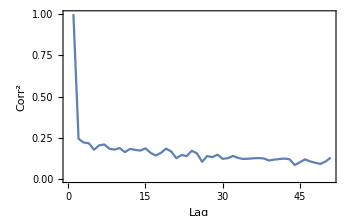

```mathematica
ListLinePlot[CorrelationFunction[Abs[returns[[All,2]]],{50}],PlotRange->Full,Frame->True,FrameLabel->{"Lag","Corr^2"}]
```

This slow decay is explained by the volatility clustering, that is the effect that price changes are usually followed by a price change of roughly the same magnitude.

Lastly there is a aggregational gaussianity on the returns, when calculated with time intervals Δt.

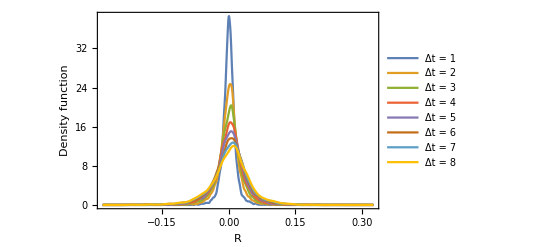

```mathematica
prices = FinancialData["^MXX",All];
Returns[x_,Δt_]:= N[Log[Take[x[[All,2]],{1+Δt,-1}]]-Log[Take[x[[All,2]],{1,-(1+Δt)}]]];
SmoothHistogram[Table[Returns[prices,Δt],{Δt,1,8}],PlotRange->Full,PlotLegends->Table["Δt = " <> ToString[i],{i,1,8}],Frame->True,FrameLabel->{"R","Density function"}]
```

As Δt increases the kurtosis of the returns converges slowly to 3, which is defined to be the kurtosis of a normal distribution.

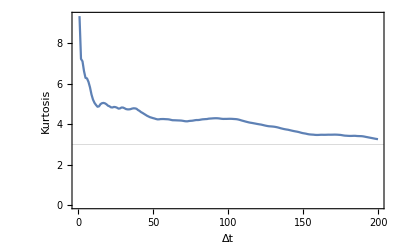

```mathematica
ListLinePlot[Table[Kurtosis[Returns[prices,Δt]],{Δt,1,200}],Frame->True,FrameLabel->{"Δt","Kurtosis"},PlotRange->Full,GridLines->{None,{3}}]
```

And lastly it’s worth mentioning the leverage effect, which states that most measures of volatility of an asset are negatively correlated with the returns of that asset. This happens because high volatility usually means a market in panic, where prices usually go down. Defining the volatility as the absolute value of the returns we get the following result.

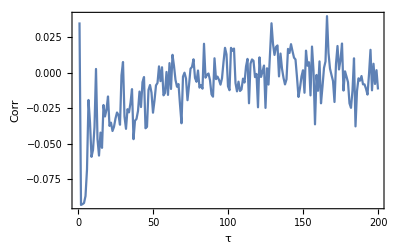

```mathematica
s = Returns[prices,1];
ListLinePlot[Table[{τ,Correlation[Abs[s[[τ;;-1]]],s[[1;;-τ]]]},{τ,1,200}],Frame->True,FrameLabel->{"τ","Corr"}]
```

## An application: designing a trading strategy

The knowledge of how the returns behave on the tails is useful to construct a simple trading strategy. Using the fact that given the fat tails big negative returns are rare events and since low prices are usually a temporary phenomenon it’s a reasonable strategy that if you invest more when prices are extremely low, eventually when the market recovers you will be able to recover the investment. This family of strategies are called mean reversion.

Let’s define the virtual trader. Let’s simplify the problem assuming that the distribution of the tails always behaves similarly.

```mathematica
prices = FinancialData["^MXX",All][[All,2]];
Returns[x_,Δt_]:= N[Log[Take[x,{1+Δt,-1}]]-Log[Take[x,{1,-(1+Δt)}]]];
posparams = FindDistributionParameters[Select[Returns[prices,1],#>0&],ParetoDistribution[k,α]];
negparams = FindDistributionParameters[-Select[Returns[prices,1],#<0&],ParetoDistribution[k,α]];
```

The virtual trader will have shares and money (will be able to have debt up to a limit). If in the current iteration there is a negative value of the return, it will buy or sell accordingly to the probability of having a value as extreme as observed.

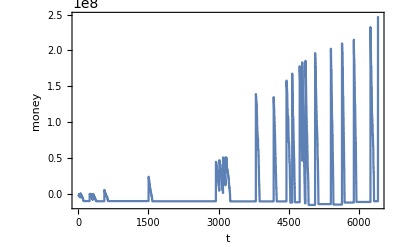

```mathematica
shares = 0;
money = 0;
ret = Returns[prices,1];
m = Table[
r = ret[[i]];
If[r<0,
p = Probability[ρ<-r,ρ\[Distributed]ParetoDistribution[k,α]/.negparams];
If[p>0.01 && money > -10^7,
buyshares = Floor[100/p];
shares+= buyshares;
money -= prices[[i+1]]*buyshares;
];

,
p = Probability[ρ<r,ρ\[Distributed]ParetoDistribution[k,α]/.posparams];
If[p<0.3,
money += prices[[i+1]]*shares;
shares = 0;
];
];
money
,{i,1,Length[ret]-1}
];
money+= prices[[-1]]*shares;
ListLinePlot[Append[m,money],PlotRange->Full,Frame->True,FrameLabel->{"t","money"}]
```

The virtual trader ends up making a reasonable amount of profit.

## A simple system with stylized facts: the game of life

One of the reasons of the relevance of stylized facts, apart from being useful tools for understanding the behavior of markets is that they allow us to construct models of financial markets under a microscopic point of view, and assess their effectiveness by checking if they are still able to reproduce the stylized facts. Many artificial stock markets have been modelled as agent based models or cellular automata models, and in fact even the game of life exhibits shares some properties with the stock markets. To demonstrate this let’s search for stylized facts on the GOL.

Let’s iterate 2000 times the game of life with a board of 200x200. The greater the board the better the results will be.

```mathematica
n =200;
gol = CellularAutomaton["GameOfLife",RandomInteger[1,{n,n}],2000];
ListAnimate[Map[ArrayPlot,Take[gol,300]]]
```

Let’s define the “center of mass” of the game of life as

```mathematica
RCM[gol_]:=1/n Sum[gol[[i,j]]({i,j}-n/2),{i,1,n},{j,1,n}];
```

Then we can get all the center of masses. It looks like a random walk.

```mathematica
rcms = Map[RCM,gol];
Animate[ListLinePlot[rcms,AspectRatio->1,Frame->True,FrameLabel->{"x","y"},Epilog->{PointSize[Large],Point[rcms[[i]]]}],{i,1,Length[rcms],1},AnimationRate->10,SaveDefinitions->True]
```

Then to construct a time series we can take the norm of the center of masses, and obtain a time series r. This r will be the observable of the system.

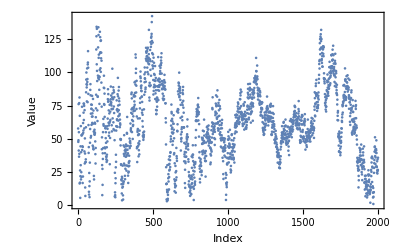

```mathematica
r = N[Map[Norm,rcms]];
ListPlot[r,Frame->True,FrameLabel->{"Index","Value"}]
```

When computing the returns a more complicated structure can be seen, indicating that this is not a simple random walk. One can check by plain sight that there is some degree of volatility clustering, so let’s proceed to check for stylized facts.

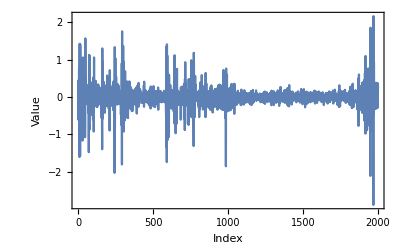

```mathematica
Returns[x_,Δt_]:= N[Log[Take[x,{1+Δt,-1}]]-Log[Take[x,{1,-(1+Δt)}]]];
ListLinePlot[Returns[r,1],Frame->True,FrameLabel->{"Index","Value"},PlotRange->Full]
```

There is aggregational gaussianity

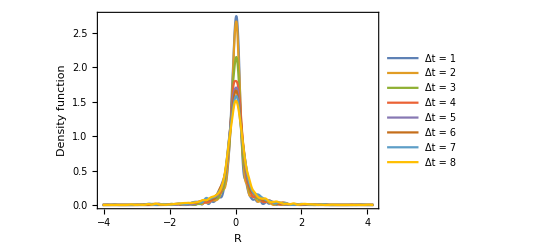

```mathematica
SmoothHistogram[Table[Returns[r,Δt],{Δt,1,8}],PlotRange->Full,PlotLegends->Table["Δt = " <> ToString[i],{i,1,8}],Frame->True,FrameLabel->{"R","Density function"}]
```

as is evidenced by the convergence of the kurtosis

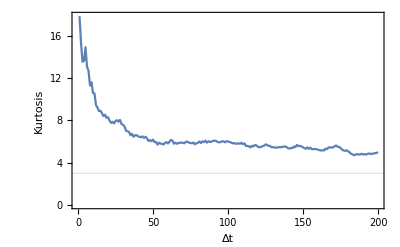

```mathematica
ListLinePlot[Table[Kurtosis[Returns[r,Δt]],{Δt,1,200}],Frame->True,FrameLabel->{"Δt","Kurtosis"},PlotRange->Full,GridLines->{None,{3}}]
```

The fat tails are a bit more tricky to visualize

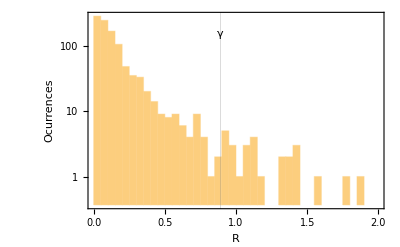

```mathematica
posValues = Select[Returns[r,1],#≥0&];
γ = LeftCutoff[posValues,0.1,1,0.01];
Histogram[posValues,ScalingFunctions->{None,"Log"},PlotRange->{{0,2},All},GridLines->{{γ},None},Epilog->{Inset[Text["γ"],{γ,5}]},Frame->True,FrameLabel->{"R","Ocurrences"}]
```

But we can just test for them

```mathematica
FindDistribution[Select[Returns[r,1],#>γ&]]
```

ParetoDistribution[7.,5.26369,2.2207,0.899226]

Slow decay of  absolute returns

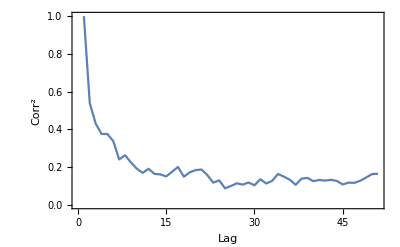

```mathematica
ListLinePlot[CorrelationFunction[Abs[Returns[r,1]],{50}],PlotRange->Full,Frame->True,FrameLabel->{"Lag","Corr^2"}]
```

and leverage effect

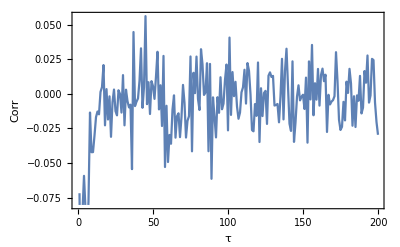

```mathematica
s = Returns[r,1];
ListLinePlot[Table[{τ,Correlation[Abs[s[[τ;;-1]]],s[[1;;-τ]]]},{τ,1,200}],Frame->True,FrameLabel->{"τ","Corr"}]
```

It seems that financial markets share many properties with a simple game of life. One question that remains open is, do they share common properties? or are stylized facts very common properties found across a wide range of complex systems that arise when carefully selecting your observable?

Further Explorations

Investigate the returns rate using other strategies

Investigate if the stylized facts still appear using other measures of returns

Authorship information

Carlos Manuel Rodríguez Martínez

2017/06/23

fis.carlosmanuel@gmail.com